```mathematica
Needs["PlotLegends`"]
Needs["NumericalCalculus`"]
```

```mathematica
v=9;
l=100;
vv=ToString[v];
ll=ToString[l];
Gappmax[l]={{0,0}};
Gapp0[l]={{0,0}};
Gappratio[l]={{0,0}};
Gappmax1[l]={{0,0}};
corr[l]={{0,0}};
corr1[l]={{0,0}};

For[i=0,i<390,i++,
d=0.005+i*0.0005;
h=0.0005;
dd=ToString[d];
Gappp[l][i]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/v"<>vv<>"-d"<>dd<>"-l"<>ll<>"k.txt",{Number,Number}];
Gapp0[l]=Append[Gapp0[l],{d,Gappp[l][i][[All,2]][[1]]}];
Gappmax[l]=Append[Gappmax[l],{d,Gappp[l][i][[All,2]][[v+1]]}];
Gappmax1[l]=Append[Gappmax1[l],{d,Gappp[l][i][[All,2]][[v]]}];
Gappratio[l]=Append[Gappratio[l],{d,(Gappp[l][i][[All,2]][[v+2]])/Gappp[l][i][[All,2]][[v+1]]}];

x=Sum[(j-1)*Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}]/Sum[Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}];
corr[l]=Append[corr[l],{d,x}];

x1=Sum[(j-1)*Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}];
corr1[l]=Append[corr1[l],{d,x1}];

]


corr[l]=Delete[corr[l],1];
corr1[l]=Delete[corr1[l],1];
Gapp0[l]=Delete[Gapp0[l],1];
Gappmax[l]=Delete[Gappmax[l],1];
Gappmax1[l]=Delete[Gappmax1[l],1];
Gappratio[l]=Delete[Gappratio[l],1];

cor2=corr1[l][[All,2]];
derr[l]=Table[{0.005+i*0.0005,(-cor2[[i+2]]+8*cor2[[i+1]]-8*cor2[[i-1]]+cor2[[i-2]])/(12*0.0005)},{i,4,Length[cor2]-2}];
```

```mathematica
ListAnimate[Table[ListPlot[Gappp[l][x],PlotRange->{{0,45},{0,0.3}},PlotLabel->0.005+x*0.0005],{x,250}]]
```

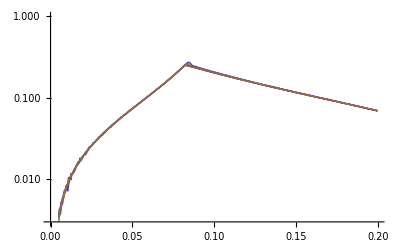

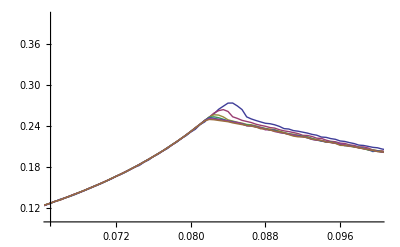

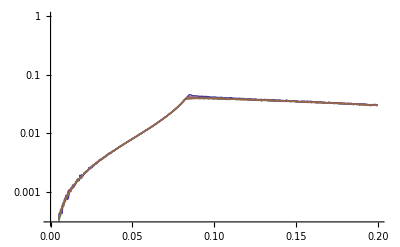

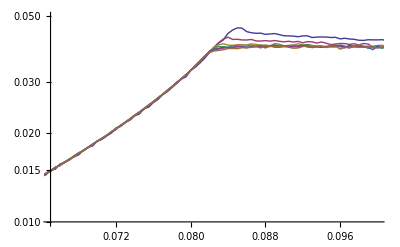

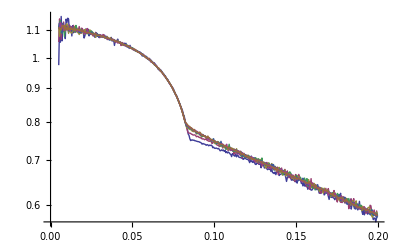

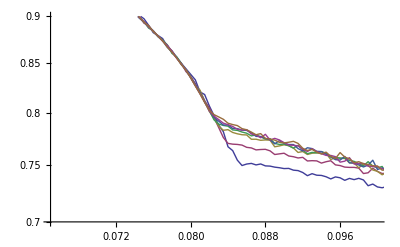

155

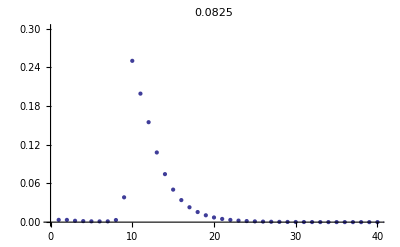

```mathematica
ListLogPlot[{Gappmax[5],Gappmax[10],Gappmax[20],Gappmax[30],Gappmax[40],Gappmax[50],Gappmax[100]},PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->True]
ListLinePlot[{Gappmax[5],Gappmax[10],Gappmax[20],Gappmax[30],Gappmax[40],Gappmax[50],Gappmax[100]},PlotRange->{{0.065,0.1},{0.1,0.4}},PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->True]
ListLogPlot[{Gappmax1[5],Gappmax1[10],Gappmax1[20],Gappmax1[30],Gappmax1[40],Gappmax1[50],Gappmax1[100]},PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->True]
ListLogPlot[{Gappmax1[5],Gappmax1[10],Gappmax1[20],Gappmax1[30],Gappmax1[40],Gappmax1[50],Gappmax1[100]},PlotRange->{{0.065,0.1},{0.01,0.05}},Joined->True,PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListLogPlot[{Gappratio[5],Gappratio[10],Gappratio[20],Gappratio[30],Gappratio[40],Gappratio[50],Gappratio[100]},PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->True]
ListLogPlot[{Gappratio[5],Gappratio[10],Gappratio[20],Gappratio[30],Gappratio[40],Gappratio[50],Gappratio[100]},PlotRange->{{0.065,0.1},{0.7,0.9}},Joined->True,PlotLegend->{"5k","10k","20k","30k","40k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

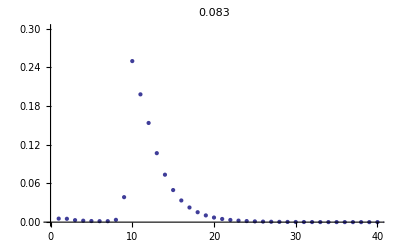

```mathematica
x=156;
ListPlot[Gappp[l][x],PlotRange->{{0,40},{0,0.3}},PlotLabel->0.005+x*0.0005]
```

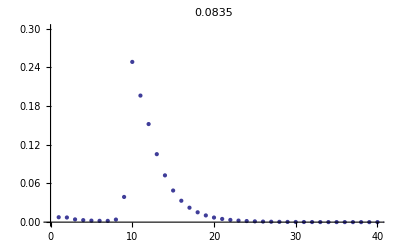

```mathematica
x=157;
ListPlot[Gappp[l][x],PlotRange->{{0,40},{0,0.3}},PlotLabel->0.005+x*0.0005]
```

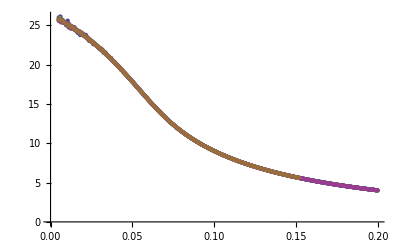

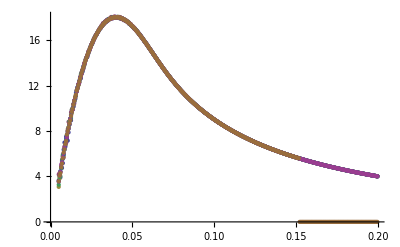

```mathematica
ListPlot[{corr[5],corr[10],corr[20],corr[30],corr[40],corr[50],corr[100]}]
ListPlot[{corr1[5],corr1[10],corr1[20],corr1[30],corr1[40],corr1[50],corr1[100]}]
```

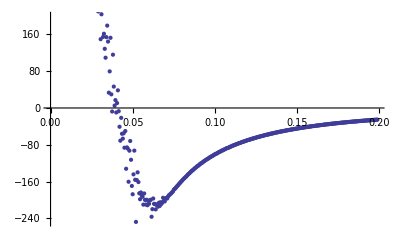

```mathematica
ListPlot[derr[50]]
```

```mathematica
icor[l]=Interpolation[corr[l]];
```

```mathematica
ider[l]=D[icor[l][x],x]
```

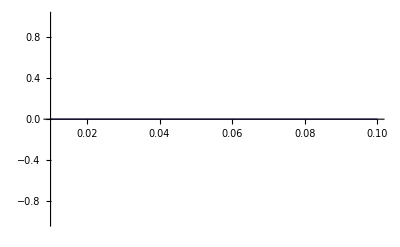

```mathematica
Plot[ND[icor[l][x],x,y],{y,0.01,0.1}]
```

```mathematica
ND[icor[l][x],,0.1]
```

0.

```mathematica
D[icor[l][x],x][0.1]
```

(∂_4.01175 1.41228×10^7)[0.1]

```mathematica
icor[l][0.05]
```

17.7943

```mathematica
f=Interpolation[corr[l]];
```

```mathematica
f[0.15]
```

5.66542

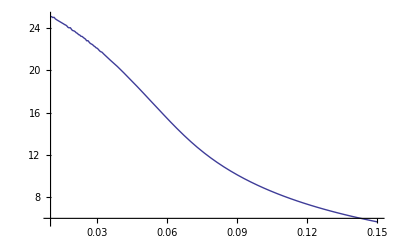

```mathematica
Plot[f[i],{i,0.01,0.15}]
```

```mathematica
g=ND[f[k],k,i]
```

-81.5839

```mathematica
de
```

```mathematica
de[l]=Table[{i*0.004,(-f[(i+2)*0.004]+8*f[(i+1)*0.004]-8*f[(i-1)*0.004]+f[(i-2)*0.004])/(12*0.004)},{i,5,40}];
f2=Interpolation[de[l]];
```

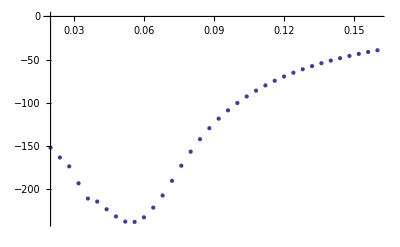

```mathematica
ListPlot[de[l]]
```

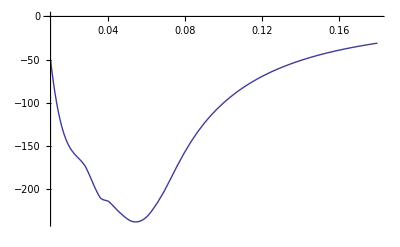

```mathematica
Plot[f2[i],{i,0.01,0.18}]
```

```mathematica
dee2[l]=Table[{i*0.004,(-f2[(i+2)*0.004]+8*f2[(i+1)*0.004]-8*f2[(i-1)*0.004]+f2[(i-2)*0.004])/(12*0.004)},{i,5,50}];
```

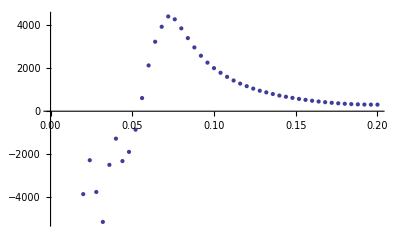

```mathematica
ListPlot[dee2[l]]
```

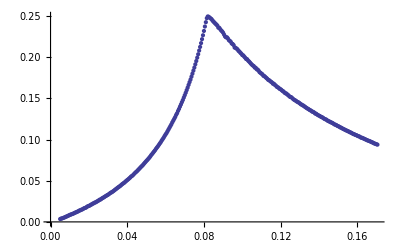

```mathematica
ListPlot[Gappmax[l]]
```

```mathematica
der2=Table[{i,ND[f[k],k,i]},{i,0.03,0.15}]
```

{{0.03,Indeterminate}}

```mathematica
de2={{0,0}};
For[i=0,i<390,i++,
d=0.01+i*0.0005;
de2=Append[de2,{d,ND[f[x],x,d]}];
]
de2=Delete[de2,1];
```

```mathematica
f[0.01]
ND[f[x],x,0.04]
```

25.1053

-206.783

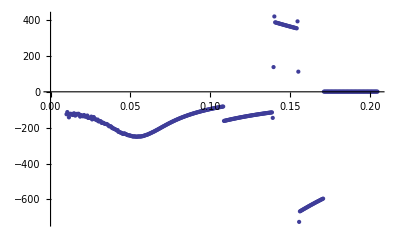

```mathematica
ListPlot[de2]
```

```mathematica
h=0.005;
e=Table[{i*0.0005,(-f[i+2h]+8*f[i+h]-8*f[i-h]+f[i-2h])/(12h)},{i,20,350}];
f2=Interpolation[de[l]];
```

```mathematica
v=9;
l=10;
vv=ToString[v];
ll=ToString[l];
Gappmax[l]={{0,0}};
Gapp0[l]={{0,0}};
Gappratio[l]={{0,0}};
Gappmax1[l]={{0,0}};
corr[l]={{0,0}};
corr1[l]={{0,0}};

For[i=0,i<150,i++,
d=0.001+i*0.001;
h=0.001;
dd=ToString[d];
Gappp[l][i]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-d"<>dd<>"-l"<>ll<>"k.txt",{Number,Number}];
Gapp0[l]=Append[Gapp0[l],{d,Gappp[l][i][[All,2]][[1]]}];
Gappmax[l]=Append[Gappmax[l],{d,Gappp[l][i][[All,2]][[v+1]]}];
Gappmax1[l]=Append[Gappmax1[l],{d,Gappp[l][i][[All,2]][[v]]}];
Gappratio[l]=Append[Gappratio[l],{d,(Gappp[l][i][[All,2]][[v+2]])/Gappp[l][i][[All,2]][[v+1]]}];

x=Sum[j*Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}]/Sum[Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}];
corr[l]=Append[corr[l],{d,x}];

x1=Sum[j*Gappp[l][i][[All,2]][[j]],{j,1,Length[Gappp[l][i]]}];
corr1[l]=Append[corr1[l],{d,x1}];

]


corr[l]=Delete[corr[l],1];
corr1[l]=Delete[corr1[l],1];
Gapp0[l]=Delete[Gapp0[l],1];
Gappmax[l]=Delete[Gappmax[l],1];
Gappmax1[l]=Delete[Gappmax1[l],1];
Gappratio[l]=Delete[Gappratio[l],1];
```

```mathematica
cor2=corr1[l][[All,2]];
derr[l]=Table[{0.005+i*0.0005,(-cor2[[i+2]]+8*cor2[[i+1]]-8*cor2[[i-1]]+cor2[[i-2]])/(12*0.0005)},{i,4,Length[cor2]-2}];
```

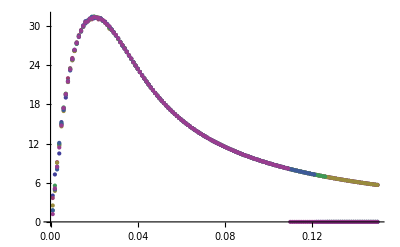

```mathematica
ListPlot[{corr1[5],corr1[10],corr1[20],corr1[30],corr1[40],corr1[50]}]
```

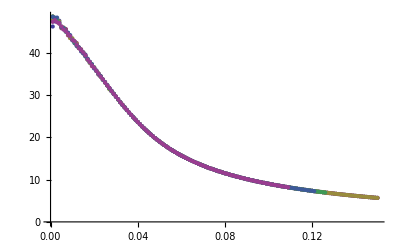

```mathematica
ListPlot[{corr[5],corr[10],corr[20],corr[30],corr[40],corr[50]}]
```

```mathematica
ListAnimate[Table[ListPlot[Gappp[l][x],PlotRange->{{0,90},{0,0.3}},PlotLabel->0.001+x*0.001],{x,150}]]
```

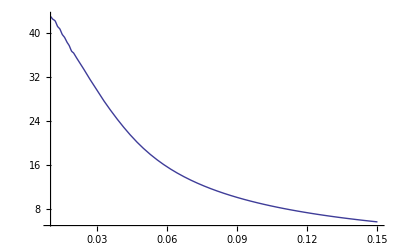

```mathematica
f=Interpolation[corr[10]];

Plot[f[i],{i,0.01,0.15}]
```

```mathematica
de[l]=Table[{i*0.004,(-f[(i+2)*0.004]+8*f[(i+1)*0.004]-8*f[(i-1)*0.004]+f[(i-2)*0.004])/(12*0.004)},{i,5,40}];
f2=Interpolation[de[l]];
```

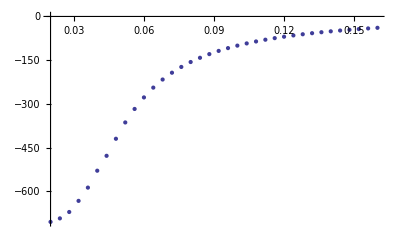

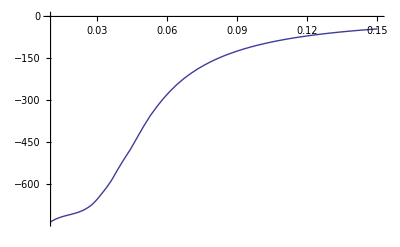

```mathematica
ListPlot[de[l]]
Plot[f2[i],{i,0.01,0.15}]
```

```mathematica
dee[l]=Table[{i*0.004,(-f2[(i+2)*0.004]+8*f2[(i+1)*0.004]-8*f2[(i-1)*0.004]+f2[(i-2)*0.004])/(12*0.004)},{i,8,38}];
```

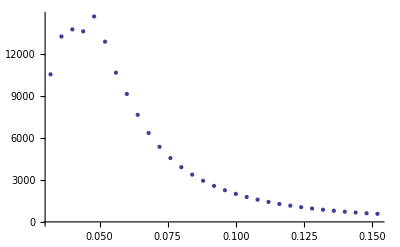

```mathematica
ListPlot[dee[l]]
```

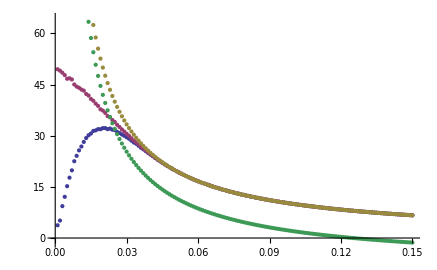

```mathematica
density=Table[{corr[10][[All,1]][[i]],1/corr[10][[All,1]][[i]]},{i,1,Length[corr[10]]}];
densityeff=Table[{corr[10][[All,1]][[i]],1/corr[10][[All,1]][[i]]-8},{i,1,Length[corr[10]]}];
ListPlot[{corr1[10],corr[10],density,densityeff}]
```

```mathematica
v=9;
l=100;
vv=ToString[v];
ll=ToString[l];
correlation[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-corr.txt",{Number,Number}];
f=Interpolation[correlation[l]];
de[l]=Table[{i*0.004,(-f[(i+2)*0.004]+8*f[(i+1)*0.004]-8*f[(i-1)*0.004]+f[(i-2)*0.004])/(12*0.004)},{i,5,35}];
f=Interpolation[de[l]];
de[l]=Table[{i*0.004,(-f[(i+2)*0.004]+8*f[(i+1)*0.004]-8*f[(i-1)*0.004]+f[(i-2)*0.004])/(12*0.004)},{i,5,35}];
```

```mathematica
ListPlot[de[l]]
```

-Graphics-

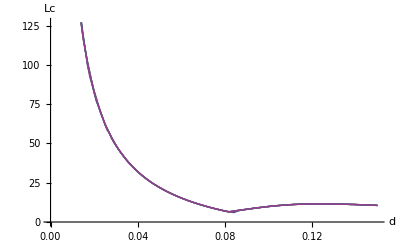

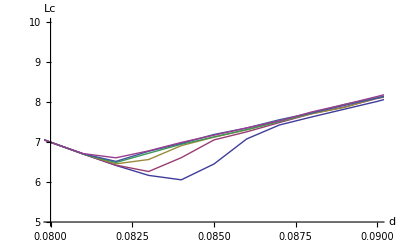

```mathematica
ListPlot[{correlation[5],correlation[10],correlation[20],correlation[30],correlation[50],correlation[100]},Joined->True,PlotLegend->{"5k","10k","20k","30k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Lc"}]
ListPlot[{correlation[5],correlation[10],correlation[20],correlation[30],correlation[50],correlation[100]},Joined->True,PlotRange->{{0.08,0.09},{5,10}},PlotLegend->{"5k","10k","20k","30k","50k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Lc"}]
```

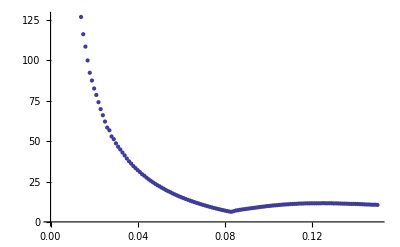

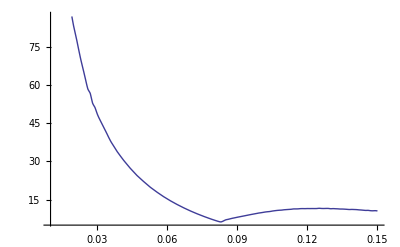

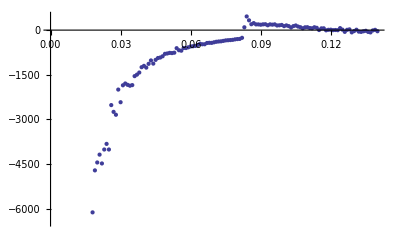

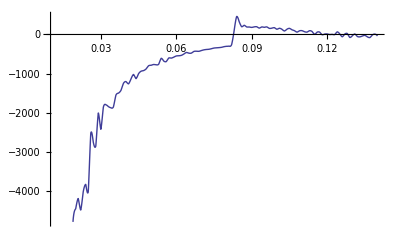

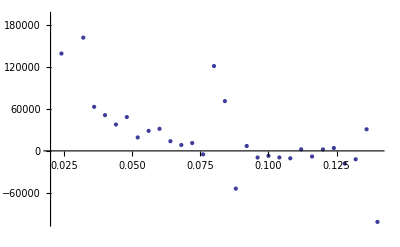

```mathematica
f=Interpolation[correlation[l]];
ListPlot[correlation[l]]
Plot[f[i],{i,0.01,0.15}]
de[l]=Table[{i*0.001,(-f[(i+2)*0.001]+8*f[(i+1)*0.001]-8*f[(i-1)*0.001]+f[(i-2)*0.001])/(12*0.001)},{i,5,140}];
f=Interpolation[de[l]];
ListPlot[de[l]]
Plot[f[i],{i,0.01,0.14}]
de[l]=Table[{i*0.004,(-f[(i+2)*0.004]+8*f[(i+1)*0.004]-8*f[(i-1)*0.004]+f[(i-2)*0.004])/(12*0.004)},{i,5,35}];
ListPlot[de[l]]
```